# Parametric Plots

## Basic Exercises

### Question Subsection

The Cycloid is the curve that is traced by a point on the outer edge of a wheel as the wheel rolls along a surface without slipping (See image below). Its parametric equations are:

x = t - sin(t)
y = 1 - cos(t)

where t stands for time. Using ParametricPlot, plot the curve from t=0 to t=20.

#### Solution

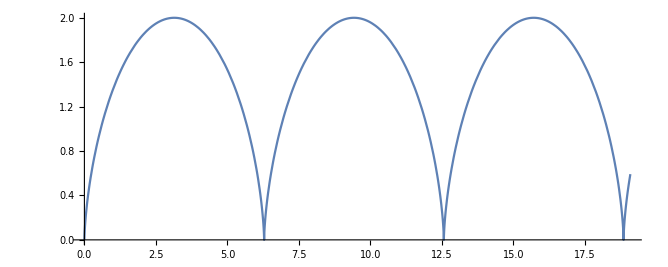

```mathematica
ParametricPlot[{t - Sin[t], 1 - Cos[t]},{t,0,20}]
```

### Question Subsection

```mathematica
?ParametricPlot
```

ParametricPlot[{f_x,f_y},{u,u_min,u_max}] generates a parametric plot of a curve with x and y coordinates f_x and f_y as a function of u. 
ParametricPlot[{{f_x,f_y},{g_x,g_y},…},{u,u_min,u_max}] plots several parametric curves. 
ParametricPlot[{f_x,f_y},{u,u_min,u_max},{v,v_min,v_max}] plots a parametric region. 
ParametricPlot[{{f_x,f_y},{g_x,g_y},…},{u,u_min,u_max},{v,v_min,v_max}] plots several parametric regions. 
ParametricPlot[…,{u,v}∈reg] takes parameters {u,v} to be in the geometric region reg.

Using the third form of ParametricPlot, we can plot a parametric region. Use this to plot a donut with outer radius of 2, and inner radius of 1.

#### Solution

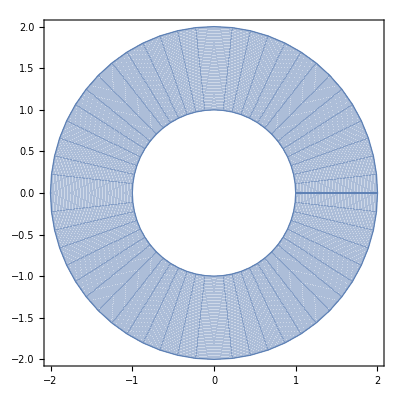

```mathematica
ParametricPlot[{r  Cos[t], r Sin[t]},{t,0,2 Pi},{r,1,2}]
```

### Question Subsection

Play around with the options of ParametricPlot to make the plot above look pretty. Specifically, add a red boundary to the region.

#### Solution

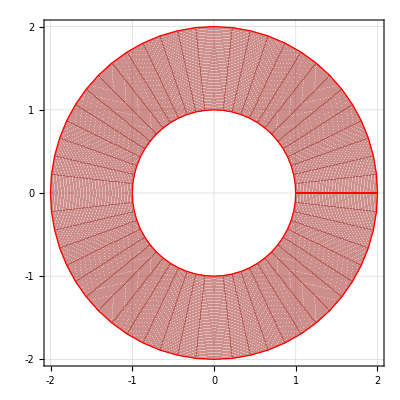

```mathematica
ParametricPlot[{r Cos[t],r Sin[t]},{t,0,2 Pi},{r,1,2},BoundaryStyle->{Thick, Red},PlotTheme->"Business",PlotStyle->12]
```

### Question Subsection

Make oval spiral that grows out of the origin and coils around itself a couple of times.

#### Solution

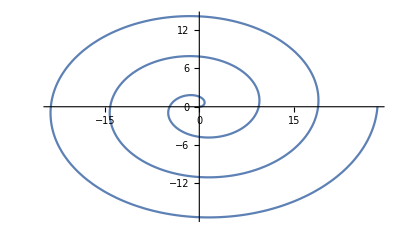

```mathematica
ParametricPlot[{1.5 t Cos[t],t Sin[t]},{t,0,6 Pi},AspectRatio->Automatic]
```

### Question Subsection

Make a spiral region that grows out of the origin and coils around itself a couple of times. Add a boundary.

#### Solution

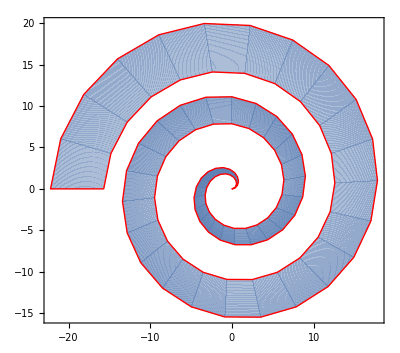

```mathematica
ParametricPlot[{Sqrt[r] t Cos[t],Sqrt[r]t Sin[t]},{t,0,5 Pi},{r,1,2},BoundaryStyle->{Thick, Red}]
```